```mathematica
"e_1"
```

# Analytical solution for the stresses in a simplified head model

Haneesh Kesari
Solid Mechanics Group
Brown University

## Panther’s strategy:

1. Map tissue strain/strain - rate to injury mechanisms
2. Map sensor (e.g.accelerometers) measurements to kinematics
3. Map head (and body) kinematics to tissue stresses and  stress-rates  or strains and strain-rates

```mathematica
Grid[{{MaTeX["\\text{Map tissue strain/strain - rate to injury mechanisms}",FontSize->28]," "},{Show[-Graphics-,ImageSize->600], }}]
```

-Graphics- |  
-Graphics- |

## Simplified head model

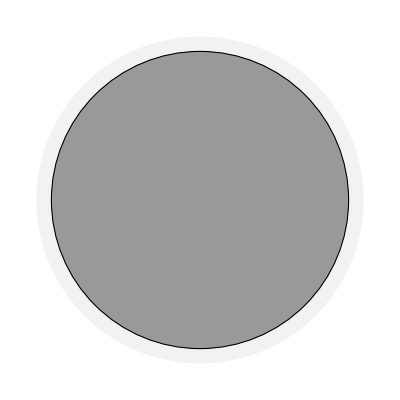
-Graphics- | -Graphics-

```mathematica
SetOptions[Style,FontFamily->"TimesNewRoman"];
SetOptions[Style,FontSize->28];
(*SetOptions[Tooltip,Background->White]*)
HeadModel=Graphics[{Tooltip[{GrayLevel[0.95],Opacity[1],Disk[{0,0},1.1]},Text[Style["Light gray region: A spherical shell, composed of a rigid material\n A model for the skull",FontSize->28,FontFamily->"Times New Roman",FontColor->GrayLevel[0.95]]],TooltipStyle->{Background->Black}],
Tooltip[{GrayLevel[0.6],Opacity[1],Disk[{0,0},1.0]},Text[Style["Dark gray region: A sphere composed of a linear elastic solid \n A model for the brain",FontSize->28,FontColor->GrayLevel[0.6],FontFamily->"Times New Roman"]],TooltipStyle->{Background->Black}],
Tooltip[{Thickness[0.002],Black,Circle[{0,0},1.0]},Text[Style["The elastic sphere is bonded to the  spherical shell",FontSize->28,FontColor->Black,FontFamily->"Times New Roman"]],TooltipStyle->{Background->White}]}];

img=-Graphics-;
Grid[{{Show[img,ImageSize->600],HeadModel}},Spacings->{1, 1}]
```

Left image from https://www.istockphoto.com/photo/human-head-brain-spine-medical-diagram-gm623931190-109575361

## Geometry and notation: reference space

Reference configuration

```mathematica
L=1;
pltSize=2.5;
SetOptions[Graphics3D,
PlotRange->{{-pltSize,pltSize},{-pltSize,pltSize},{-pltSize,pltSize}}];
objs1=PlotTriad[{{{0,0,0},"\\boldsymbol{O}_{\\rm R}"},
{{2,0,0},"\\boldsymbol{E}_1"},{{0,2,0},"\\boldsymbol{E_2}"},{{0,0,2},"\\boldsymbol{E}_3"}},{Text[MaTeX["\\mathbb{E}_{R}",FontSize->28],{-1.5,-1.5,-1.5}],{Opacity[0.01],Blue,EdgeForm[Dashed],Cube[{0,0,0},4.5]}},Origin->{0,0,0},WithLines->True,ϵ->.3,MaTeXFontSize->18,PointSize->0.01];
AppendTo[objs1,{White,Opacity[2],Lighting->"Neutral",Sphere[{0,0,0},1]}];
AppendTo[objs1,{Red,PointSize[0.02],Point[{-1/√3,-1/√3,1/√3}]}];
AppendTo[objs1,Text[MaTeX["\\boldsymbol{X}",FontSize->18],{-1/√3,-1/√3,1/√3}+{-0.2,-0.2,0.1}]];
With[{pltSize=2.5},
Manipulate[Graphics3D[objs1[[1;;i]],PlotRange->{{-pltSize,pltSize},{-pltSize,pltSize},{-pltSize,pltSize}},Boxed->False,ImageSize->600],{i,1,Length[objs1],1}]]
```

## Position of a material particle in the reference space (𝔼_R) is taken as the particle’s name

Reference configuration

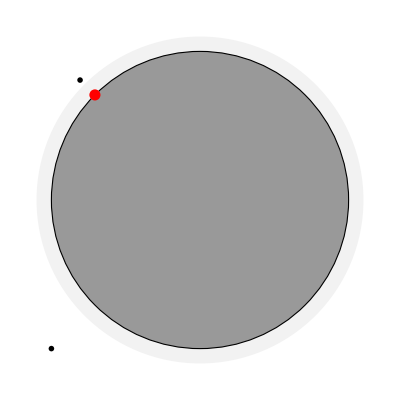

```mathematica
Show[{HeadModel,
Graphics[{Text[MaTeX["\\mathbb{E}_{R}",FontSize->28],{-1.0,-1.0}],
{Red,PointSize[0.02],Point[{-1/√2,1/√2}]},Text[MaTeX["\\boldsymbol{X}",FontSize->28],{-1/√2,1/√2}+{-0.1,0.1}]}]
}]
```

```mathematica
MaTeX["\\boldsymbol{X}=X_{1}\\boldsymbol{E}_1+X_{2}\\boldsymbol{E}_2+X_{3}\\boldsymbol{E}_3",FontSize->28]
```

-Graphics-

## Reference space (𝔼_R) and physical space ( 𝔼 )

```mathematica
Remove["Global`objs2"]
objs2={};
With[{origin={10,10,0},pltSize=3.5},
SetOptions[Graphics3D,
PlotRange->{{-pltSize,pltSize+15},{-pltSize,pltSize+15},{-pltSize-5,pltSize+10}}];
objs2=PlotTriad[{{{2,0,0},"\\boldsymbol{e}_1"},{{0,2,0},"\\boldsymbol{e_2}"},{{0,0,2},"\\boldsymbol{e}_3"}},Fold[Prepend,DeleteCases[objs1,x_Text],
{
Text[MaTeX["\\mathbb{E}",FontSize->18],origin-{1,1,1}],{EdgeForm[Dashed],Opacity[0.01],Blue,Cube[origin,10]}}],Origin->origin,WithLines->True,ϵ->0.2,PointSize->0.005,MaTeXFontSize->18];

AppendTo[objs2,{Lighting->"Neutral",Opacity[0.8],White,Sphere[origin,1]}];
AppendTo[objs2,{Red,PointSize[0.02],Point[{10,10,0}+{-1/√3,-1/√3,1/√3}]}];
Manipulate[Show@Graphics3D[objs2[[1;;i]],Boxed->False,ImageSize->600],{i,1,Length[objs2],1}]]
```

```mathematica
CellPrint[Style[MaTeX["\\begin{aligned}
\\boldsymbol{x}_{\\tau}(\\boldsymbol{X})=&\\text{position of the material particle}~\\boldsymbol{X}~\\\\
&\\text{in}~\\mathbb{E}~\\text{at the time instance}~\\tau
\\end{aligned}",FontSize->38],TextAlignment->Center]]
```

## Deformation mapping

```mathematica
CellPrint[Style[MaTeX["\\begin{aligned}
\\boldsymbol{x}_{\\tau}(\\boldsymbol{X})=&\\text{position of the material particle}~\\boldsymbol{X}~\\\\
&\\text{in}~\\mathbb{E}~\\text{at the time instance}~\\tau\\\\
x_{1\\tau}(X_1,X_2,X_3)=&X_1+U_{1\\tau}(X_1,X_2,X_3),\\\\
x_{2\\tau}(X_1,X_2,X_3)=&X_2+U_{2\\tau}(X_1,X_2,X_3),\\\\
x_{3\\tau}(X_1,X_2,X_3)=&X_3+U_{3\\tau}(X_1,X_2,X_3).
\\end{aligned}",FontSize->38],TextAlignment->Center]]
```

-Graphics-

## Deformation mapping for non-rotatory motion

```mathematica
(*Manipulate[With[{origin={10,10,0}},
Graphics3D[Append[DeleteCases[objs2[[1;;-2]],x_Text],
sph[τ,{10,10,0}]],Boxed->False,ImageSize->600]],{τ,0,10}]
*)
With[{origin={10,10,0}},
Manipulate[Show[sph[τ,{10,10,0},1.1],Graphics3D[DeleteCases[objs2[[1;;-1]],x_Text]],PlotRange->{{-2,18},{-10,20},{-5,5}},Boxed->False,ImageSize->800],{τ,0,5}]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

## Deformation mapping for non-rotatory motion

Deformation map of material particles in the shell/skull

```mathematica
CellPrint[Style[MaTeX["\\begin{aligned}
x_{1\\tau}(X_1,X_2,X_3)=&X_1-c_1(\\tau),\\\\
x_{2\\tau}(X_1,X_2,X_3)=&X_2-c_2(\\tau),\\\\
x_{3\\tau}(X_1,X_2,X_3)=&X_3-c_3(\\tau).
\\end{aligned}",FontSize->38],TextAlignment->Center]]
```

-Graphics-

## Deformation mapping for non-rotatory motion

Deformation map of material particles in the elastic sphere (brain)

```mathematica
CellPrint[Style[MaTeX["\\begin{aligned}
x_{1\\tau}(X_1,X_2,X_3)=&X_1-c_1(\\tau)+u_{\\tau 1}(X_1,X_2,X_3),\\\\
x_{2\\tau}(X_1,X_2,X_3)=&X_2-c_2(\\tau)+u_{\\tau 2}(X_1,X_2,X_3),\\\\
x_{3\\tau}(X_1,X_2,X_3)=&X_3-c_3(\\tau)+u_{\\tau 3}(X_1,X_2,X_3).
\\end{aligned}",FontSize->38],TextAlignment->Center]]
```

-Graphics-

## Cauchy momentum equations inside the sphere

Governing equation inside the sphere

```mathematica
CellPrint[Style[MaTeX["\\begin{aligned}
(\\lambda+\\mu)u_{\\tau k,ki}[(X_{j})]+\\mu u_{\\tau i,kk}[(X_{j})]&=\\rho c''_{i}(\\tau)~\\\\   &\\quad \\quad \\forall~(X_{j})\\in \\mathcal{B}_{0}
\\end{aligned}",FontSize->38],TextAlignment->Center]]
```

Boundary conditions

```mathematica
CellPrint[Style[MaTeX["\\begin{aligned}
u_{\\tau i}[(X_{j})]&=0\\\   &\\quad \\quad \\forall~(X_{j})\\in \\partial \\mathcal{B}_{0}
\\end{aligned}",FontSize->38],TextAlignment->Center]]
```

## Solution

#### Spherical co-ordinates

## Solution

#### Stress Field

```mathematica
{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}//MatrixForm
```

(-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-)

```mathematica
{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}//MatrixForm
```

## Solution

#### Strain Field

(-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-)

Subroutines

```mathematica
Remove["Global`*"]
<<MaTeX`
L=1;
ClearAll[PlotTriad]
Options[PlotTriad]={WithLines->False,Origin->{0,0,0},ϵ->0.2,MaTeXFontSize->28,PointSize->0.002};
PlotTriad[pointsDataInput_:{{{L,0,0},"\\boldsymbol{x}"},{{0,1,0},"\\boldsymbol{y}"}},objectsInput_:{},OptionsPattern[]]:=Module[{pts,SpaceName,Sph,objects,Events,pointsData,pointLabels,styledPoints,styledLinePoints,OriginCoords,lines},
OriginCoords=OptionValue[Origin];
pts=OptionValue[PointSize];
lines=OptionValue[WithLines];
pointsData={(#[[1]]+OriginCoords),#[[2]]} &/@pointsDataInput;
styledPoints={PointSize[0.02],Point[#]} &/@pointsData[[;;,1]];
styledLinePoints={Line[{OriginCoords,#}],
{PointSize[pts],Point[#]}} &/@pointsData[[;;,1]];
pointLabels=
Text[MaTeX[#[[2]],FontSize->OptionValue[MaTeXFontSize]],(#[[1]])+OptionValue[ϵ]((#[[1]])-OriginCoords)-OptionValue[ϵ]{L,0,0}] &/@pointsData;
objects={objectsInput};
Do[AppendTo[objects,If[OptionValue[WithLines],styledLinePoints[[i]],styledPoints[[i]]]];AppendTo[objects,pointLabels[[i]]],{i,1,Length[styledPoints]}];
objects
]

logos={Rotate[-Graphics-,π/2],Rotate[-Graphics-,π/2],Rotate[-Graphics-,π/2]};
```

Remove::rmptc: Symbol xOnePixelIsSoManyMicrons is Protected and cannot be removed.

Remove::rmptc: Symbol yOnePixelIsSoManyMicrons is Protected and cannot be removed.

Remove::rmptc: Symbol zOnePixelIsSoManyMicrons is Protected and cannot be removed.

General::stop: Further output of Remove::rmptc will be suppressed during this calculation.

```mathematica
CreatePalette@Grid[
  {{Button["Hide Inputs", Module[{nb}, nb = SelectedNotebook[];
      NotebookFind[SelectedNotebook[], "Input", All, CellStyle];
      SetOptions[NotebookSelection[nb], CellOpen -> False, 
       ShowCellBracket -> False]]],
    
    Button["Show Inputs", Module[{nb}, nb = SelectedNotebook[];
      NotebookFind[SelectedNotebook[], "Input", All, CellStyle];
      SetOptions[NotebookSelection[nb], CellOpen -> True, 
       ShowCellBracket -> True]]]},
   {
    Button["Hide Output", Module[{nb}, nb = SelectedNotebook[];
      NotebookFind[SelectedNotebook[], "Output", All, CellStyle];
      SetOptions[NotebookSelection[nb], CellOpen -> False, 
       ShowCellBracket -> False]]],
    
    Button["Show Output", Module[{nb}, nb = SelectedNotebook[];
      NotebookFind[SelectedNotebook[], "Output", All, CellStyle];
      SetOptions[NotebookSelection[nb], CellOpen -> True, 
       ShowCellBracket -> True]]]},
   {
    Button["Hide Text", Module[{nb}, nb = SelectedNotebook[];
      NotebookFind[SelectedNotebook[], "Text", All, CellStyle];
      SetOptions[NotebookSelection[nb], CellOpen -> False, 
       ShowCellBracket -> False]]],
    
    Button["Show Text", Module[{nb}, nb = SelectedNotebook[];
      NotebookFind[SelectedNotebook[], "Text", All, CellStyle];
      SetOptions[NotebookSelection[nb], CellOpen -> True, 
       ShowCellBracket -> True]]]
    },
   
   
   
   {
    Button["Delete Output", Module[{nb}, nb = SelectedNotebook[];
      NotebookDelete@
       Cells[nb, CellStyle -> "Output" || "Print" || "Echo"]]]
    }
   }]
   
   
sph[τ_,origin_,r_:1]:=Module[{},ParametricPlot3D[origin+c[τ]+r{ Sin[v]Cos[u],Sin[v] Sin[u],Cos[v]},{v,0,Pi},{u,0,2π},PlotStyle->Directive[Specularity[White,30],Texture[logos[[-1]]]],TextureCoordinateFunction->({#4,2#5}&),Lighting->"Neutral",Mesh->None,Boxed->False,Axes->False]]
c[τ_]:={τ Cos[τ],τ Sin[τ],τ};
```

cuzgd_shm111FrontEndObject[LinkObject["cuzgd_shm", 3, 1]]111Untitled-14

```mathematica
Manipulate[
Which[
type==1,
Show[{
Graphics3D[{Blue,Thick,Line[{{a,0,0},{a,b,0}}],Red,Line[{{0,b,0},{a,b,0}}],Darker@Green,Line[{{a,b,0},{a,b,c}}]},ImageSize->400{1,1},Ticks->None,Axes->True,Boxed->False,AxesOrigin->{0,0,0},PlotRange->{{-5,5},{-5,5},{-5,5}},AxesStyle->Gray,AspectRatio->1],
Graphics3D[{{Opacity[.1],EdgeForm[LightGray],Cuboid[{0,0,0},{a,b,c}]},Black,Sphere[{a,b,c},.1],Style[Text[Row[{"(",Style["x",Italic], ", ",Style["y",Italic], ", ",Style["z",Italic],")"}],{a,b,c+1}],16,Italic],Style[Text["x",{a/2,b+1,0}],16,Red,Italic],
Style[Text["y",{a-.75,b/2,0}],16,Blue,Italic],Style[Text["z",{a+.5,b,c/2}],16,Darker@Green,Italic]}]
}],
type==2,
Show[{
ParametricPlot3D[{(4r/4)*Cos[π*t],(4r/4)*Sin[π*t],0},{t,0,If[θ==0,.0001,θ/π]},PlotStyle->Directive[Blue,Thick],PlotRange->{{-5,5},{-5,5},{-5,5}},ImageSize->400{1,1},Mesh->None,PerformanceGoal->Quality,Ticks->None,Axes->True,AxesStyle->Gray,Boxed->False,AxesOrigin->{0,0,0},AspectRatio->1],
ParametricPlot3D[{t*Cos[θ],t*Sin[θ],0},{t,0,r},PlotStyle->Directive[Red,Thick]],
ParametricPlot3D[{r*Cos[θ],r*Sin[θ],k},{k,0,z},PlotStyle->Directive[Darker@Green,Thick]],
Graphics3D[{{Opacity[.1],EdgeForm[LightGray],Cylinder[{{0,0,0},{0,0,z}},r]},Black,Sphere[{r*Cos[θ],r*Sin[θ],z},.1],Style[Text[Row[{"(",Style["r",Italic],", θ, ",Style["z",Italic],")"}],{(r+1)*Cos[θ],(r+1)*Sin[θ],z+1}],16],Style[Text["θ",{(r+1)*Cos[θ]+.4,(r+1)*Sin[θ]+.4,0}],16,Blue],
Style[Text["r",{(r-1)*Cos[θ],(r-1)*Sin[θ],.5}],16,Red,Italic],Style[Text["z",{(r-.25)*Cos[θ],(r-.25)*Sin[θ],3z/4}],16,Darker@Green,Italic]}]
}],
type==3,
Show[{
ParametricPlot3D[{r*Sin[ϕ]*Cos[theta],r*Sin[ϕ]*Sin[theta],r*Cos[ϕ]},{r,0,ρ},PlotStyle->Directive[Thick,Red],PlotRange->{{-5,5},{-5,5},{-5,5}},ImageSize->400{1,1},Mesh->None,Ticks->None,Axes->True,AxesStyle->Gray,Boxed->False,AxesOrigin->{0,0,0},AspectRatio->1,PerformanceGoal->Quality],
ParametricPlot3D[{ρ*Sin[p]*Cos[theta],ρ*Sin[p]*Sin[theta],ρ*Cos[p]},{p,0,ϕ},PlotStyle->Directive[Thick,Darker@Green]],
ParametricPlot3D[{ρ*Sin[p]*Cos[theta],ρ*Sin[p]*Sin[theta],ρ*Cos[p]},{p,ϕ,If[ϕ==π/2,0,π/2]},PlotStyle->Directive[Dashed,Darker@Green]],
ParametricPlot3D[{ρ*Sin[π/2]*Cos[t],ρ*Sin[π/2]*Sin[t],ρ*Cos[π/2]},{t,0,theta},PlotStyle->Directive[Thick,Blue]],
Graphics3D[{{Opacity[.1],Sphere[{{0,0,0}},ρ]},Black,Sphere[{ρ*Sin[ϕ]*Cos[theta],ρ*Sin[ϕ]*Sin[theta],ρ*Cos[ϕ]},.1],
{Blue,Line[{{0,0,0},ρ{Cos[theta],Sin[theta],0}}]},
Style[Text["(R, ϕ, θ)",{(ρ+1)*Sin[(ϕ+.2)]*Cos[theta],(ρ+1)*Sin[(ϕ+.2)]*Sin[theta],(ρ+1)*Cos[(ϕ+.2)]}],16],
Style[Text["R",{ρ/2*Sin[(ϕ+.25)]*Cos[theta],ρ/2*Sin[(ϕ+.25)]*Sin[theta],ρ/2*Cos[(ϕ+.25)]}],16,Red],
Style[Text["ϕ",{(ρ+.5)*Sin[ϕ/2]*Cos[theta],(ρ+.5)*Sin[ϕ/2]*Sin[theta],(ρ+.5)*Cos[ϕ/2]}],16,Darker@Green],
Style[Text["θ",{(ρ+.75)*Sin[π/2]*Cos[theta/2],(ρ+.75)*Sin[π/2]*Sin[theta/2],(ρ+.75)*Cos[π/2]}],16,Blue]
}]
}]],
{{type,1,"coordinate system"},{1->"rectangular",2->"cylindrical",3->"spherical"},ControlPlacement->Top},
OpenerView[{"rectangular",Column[{
Control[{{a,3,Style["x",Italic]},-4,4,.2,Appearance->"Labeled",ImageSize->Tiny}],
Control[{{b,3,Style["y",Italic]},-4,4,.2,Appearance->"Labeled",ImageSize->Tiny}],
Control[{{c,3,Style["z",Italic]},-4,4,.2,Appearance->"Labeled",ImageSize->Tiny}],Spacer[150]
}]},Dynamic[If[type==1,True,False]],Enabled->False],
OpenerView[{"cylindrical",Column[{
Control[{{r,3},.01,4,Appearance->"Labeled",ImageSize->Tiny}],
Control[{{θ,π/4},0,2π,π/100,Appearance->"Labeled",ImageSize->Tiny}],
Control[{{z,3},-4.9,4.9,.2,Appearance->"Labeled",ImageSize->Tiny}],Spacer[150]
}]},Dynamic[If[type==2,True,False]],Enabled->False],
OpenerView[{"spherical",Column[{
Control[{{ρ,3},.01,5,Appearance->"Labeled",ImageSize->Tiny}],
Control[{{ϕ,π/4},π/100,π,π/100,Appearance->"Labeled",ImageSize->Tiny}],
Control[{{theta,0.1,"θ"},0,2π,π/100,Appearance->"Labeled",ImageSize->Tiny}],Spacer[150]
}]},Dynamic[If[type==3,True,False]],Enabled->False],
ControlPlacement->Left,
AutorunSequencing->{1}]
```

```mathematica
"σ"
```